```mathematica
Integrate[Exp[1 - A Cos[θ] - B Sin[θ] +C],θ]
```

∫ⅇ^(1+C-A Cos[θ]-B Sin[θ])ⅆθ

```mathematica
Integrate[Exp[((A- Cos[θ] )^2+ (B- Sin[θ])^2 )/C],{θ,0,2π}]
```

$Aborted

```mathematica
Integrate[Exp[ A Cos[θ] + B Sin[θ] +Const],{θ,0,2π}]
```

2 ⅇ^Const π Hypergeometric0F1Regularized[1,25/2]

```mathematica
Integrate[Exp[ 10 Cos[θ] + 20 Sin[θ] +1],{θ,0,2π}]
```

2 ⅇ π Hypergeometric0F1Regularized[1,125]

```mathematica
A = -5; B=2; Const= -3;
NIntegrate[Exp[ A Cos[θ] +B Sin[θ] +Const],{θ,0,2π}]
N[2 π Exp[Const] BesselI[0,√(A^2+B^2)]]
```

12.0406

12.0406

```mathematica
σ = 0.2;
x1=1;
x2=0;
xD2 = 0;
NIntegrate[Exp[-((Sin[θ] - x2)^2+(Cos[θ]-x1)^2 + xD2)/(2σ^2) ],{θ,0,2π}]
N[2π Exp[-(1+x1^2+x2^2+xD2)/(2σ^2)]BesselI[0,√((x1^2+x2^2)/σ^4)]]
```

0.503891

0.503891

```mathematica
N[2 π Exp[-10] BesselI[0,√(5^2+5^2)],20]
```

0.051363552186599782073

```mathematica
f[A_]:=2 ⅇ^(1+C) π BesselI[0,√(A^2+B^2)]
FullSimplify[Derivative[f[A],A]]
```

Derivative[2 ⅇ^(1+C) π BesselI[0,√(A^2+B^2)],A]

```mathematica
BesselI[0,0]
```

1

```mathematica
FullSimplify[Derivative[BesselI[0,x],x]]
```

Derivative[BesselI[0,x],x]

```mathematica
Derivative[BesselI[0,x],x]/. x->0.5
```

Derivative[1.06348,0.5]

```mathematica
D[BesselI[0,x],x]/. x->2.5
```

2.51672

```mathematica
BesselI[1,x]/.x->2.5
```

2.51672

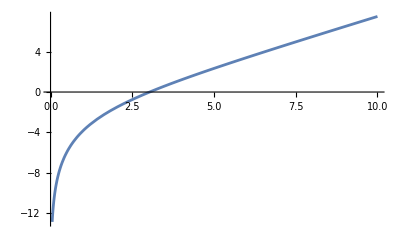

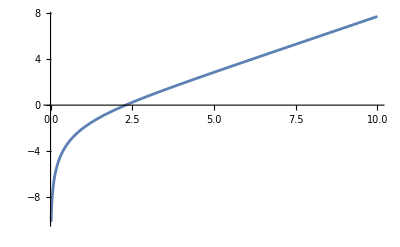

```mathematica
Plot[Log[BesselI[3,x]],{x,0,10}]
Plot[Log[BesselI[2,x]],{x,0,10}]
```

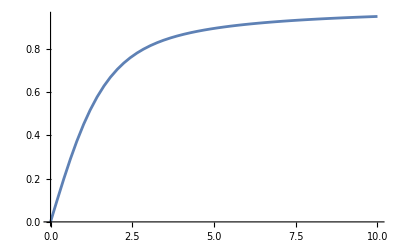

```mathematica
Plot[BesselI[-1,x]/BesselI[0,x],{x,0,10}]
```

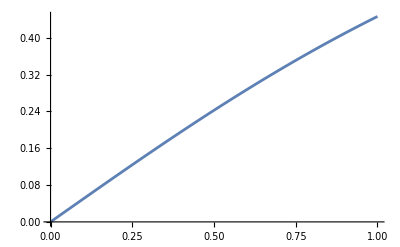

```mathematica
Plot[BesselI[1,x]/BesselI[0,x],{x,0,1}]
```

```mathematica
Plot[x(1-BesselI[2,x]/BesselI[0,x])/2,{x,0,1}]
```

-Graphics-

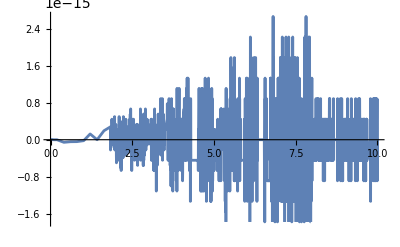

```mathematica
Plot[BesselI[1,x]/BesselI[0,x]-x/2+x BesselI[2,x]/(2 BesselI[0,x]),{x,0,10}]
```

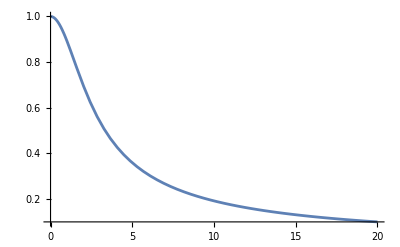

```mathematica
Plot[1 - BesselI[2,x]/( BesselI[0,x]),{x,0,20}]
```

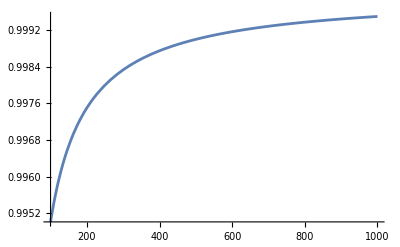

```mathematica
Plot[Exp[-ArcSinh[1/x]+Sqrt[x^2+1]-x],{x,100,1000}]
```

0.9

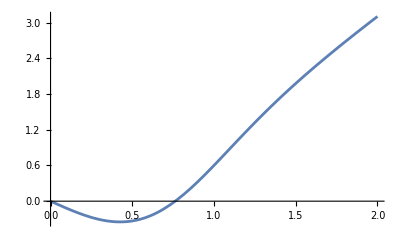

```mathematica
σ=.9
Plot[-(x/σ^2)+(2x/σ^4) BesselI[1,x^2/σ^4]/BesselI[0,x^2/σ^4],{x,0,2}]
```

### Plot of density along x1 axis

0.05

General::munfl: Exp[-999.935] is too small to represent as a normalized machine number; precision may be lost.

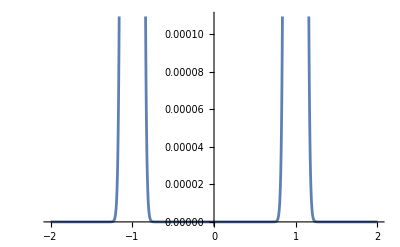

```mathematica
σ=.05
Plot[Exp[-(1+x^2)/(2σ^2)]BesselI[0,x/σ^2],{x,-2,2}]
```

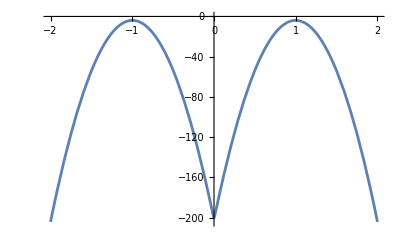

```mathematica
Plot[-(1+x^2)/(2σ^2)+Log[BesselI[0,x/σ^2]],{x,-2,2}]
```

### Plot of score along x1 axis

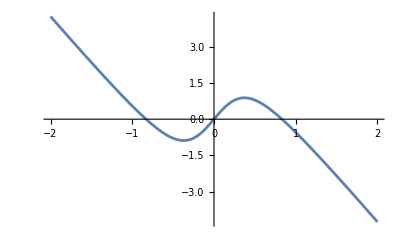

```mathematica
σ=.5;
Plot[-(x)/(σ^2)+1/σ^2 BesselI[1,x/σ^2]/BesselI[0,x/σ^2],{x,-2,2}]
```

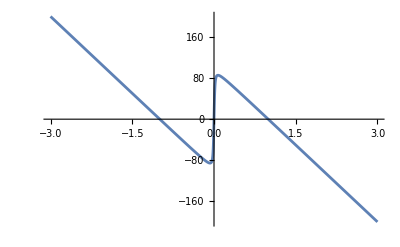

```mathematica
σ=.1;
Plot[-x/σ^2+1/σ^2*BesselI[1,x/σ^2]/BesselI[0,x/σ^2],{x,-3,3}]
```

```mathematica
Plot[Log[BesselI[0,x/σ]]]
```

```mathematica
ClearAll[x1,x2,σ];
D[√((x1^2+x2^2)/σ^4),x1]
```

x1/(√((x1^2+x2^2)/σ^4) σ^4)